```mathematica
def: y(t) e reshenie na dy/dx = f(t,y) v intervala  I ako y'(t) = f(f,y(t)) v I.
```

```mathematica
zad; Proverete ,4e y(t) = C(t^2 +1)^-2 + t^2 +1 e reshenie na dy/dx + (4t/t^2 +1)*y=6y, t prinadleji na R
Na4ertaite resheniqta za stoinosti na C = -4,-2,0,2,4
```

```mathematica
y[t_]:=c(t^2 +1)^(-2) + t^2 +1
Simplify[y'[t] + ((4t)/(t^2 + 1))*y[t]]
```

6 t

{1+t^2-4/((1+t^2)^2),1+t^2-2/((1+t^2)^2),1+t^2,1+t^2+2/((1+t^2)^2),1+t^2+4/((1+t^2)^2)}

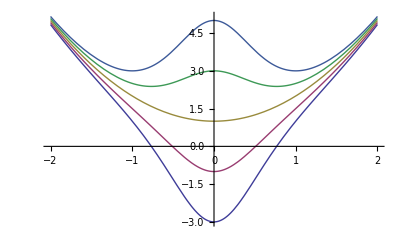

```mathematica
y[t] /. c-> {-4,-2,0,2,4} //zamesti tova koeto sledva v y (/.)
Plot[Evaluate[%],{t,-2,2}]
```

```mathematica
def: na4alna zada4a ot 1vi red se sustoi ot ody ot 1vi red i na4alno uslovie ot vida y(Subscript[t, 0]) = Subscript[y, 0]
dy/dx = f(t,y)
y(Subscript[t, 0]) = Subscript[y, 0]
Na4alnoto uslovie "izbira" edno ot bezkraino-mnogoto reshenia na ody, po-specialno reshenieto, koeto minava prez to4ka (Subscript[t, 0], Subscript[y, 0])

zad. Proverete , 4e y= 10/(1+c*e^-t/2) e reshenie na dy/dt=y/20(10-y)
za vsqka const. c prinadleji na R. Sled tova na4ertaite reshenieto na na4alnata zada4a dy/dx-y/20(10-y)
y(0) = 2



y[t_]:=10/(1+c*ⅇ^(-t/2))
Simplify[y'[t] - (y[t])*(10-y[t])/20]
```

0

Set::write: "
StyleBox[\"\\\"<Tag >\\\"\", \"MT\"]
StyleBox[\"Times\", \"MT\"]
StyleBox[\"\\\"< in >\\\"\", \"MT\"]
StyleBox[
RowBox[{\"def\", \":\", 
RowBox[{\"i\", \" \", \"na4alna\", \" \", \"na4alno\", \" \", \"ody\", \" \", \"ot\", \" \", \"ot\", \" \", \"ot\", \" \", \"ot\", \" \", 
RowBox[{\"«\", \"11\", \"»\"}]}]}], \"MT\"]
StyleBox[\"\\\"< is Protected.>\\\"\", \"MT\"] (*ButtonBox[

```mathematica
Subscript[y, 0]
Solve[y[0]==2,c]
```

y_0

{{c→4}}

```mathematica
y[t]=y[t]/.%
```

```mathematica
{10/(1+4 ⅇ^(-t/2))}
```

```mathematica
Plot[y[t],{t,-10,15}]
```

-Graphics-